Součinnové pravidlo - grafické vykreslení
Autor: David Poledne
Datum: 6. května 2025

Popis:
Tento skript graficky vykresluje uzly součinnového pravidla pro daný řád d na trojúhelníku s vrcholy vertex1, vertex2 , vertex3.

Řád kvadratury: 5

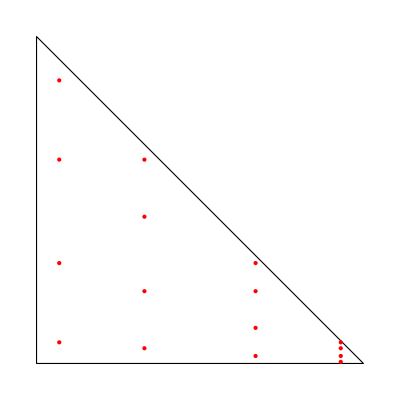

```mathematica
Remove["Global`*"]

(*Řád kvadratury *)
d=5;

(*Trojúhelník přes který se integruje*)
vertex1={0,0};
vertex2={0,1};
vertex3={1,0};
verticesPoints={vertex1,vertex2,vertex3};

Row[{"Řád kvadratury: ",d}]
(*Počet uzlů v jedné dimenzi*)
n=Ceiling[(2+d)/2];

(*Určení uzlů v jedné dimenzi*)
solutionSolve=Solve[LegendreP[n,x]==0];
solution=Table[x/.solutionSolve[[i]],{i,1,n}];
nodes=Table[{solution[[i]],solution[[j]]},{i,1,n},{j,1,n}];
nodes=Flatten[nodes,1];
nodesTransformed=Table[{(1+nodes[[i]][[1]])/2,(1-nodes[[i]][[1]])(1+nodes[[i]][[2]])/4},{i,1,Length[nodes]}];

(*Kartézské souřadnice uzlů pro grafické zobrazení*)
nodesCartes=Table[{nodesTransformed[[i]][[1]]vertex3[[1]]+nodesTransformed[[i]][[2]]vertex1[[1]]+(1-nodesTransformed[[i]][[1]]-nodesTransformed[[i]][[2]])vertex2[[1]],nodesTransformed[[i]][[1]]vertex3[[2]]+nodesTransformed[[i]][[2]]vertex1[[2]]+(1-nodesTransformed[[i]][[1]]-nodesTransformed[[i]][[2]])vertex2[[2]]},{i,1,Length[nodesTransformed]}];

(*Grafické vykreslení uzlů*)
Graphics[{EdgeForm[Black],FaceForm[],Polygon[verticesPoints],Red,PointSize[Large],Point[nodesCartes] }]
```